## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; Q=0.999; r1 = 40; mu = 0.1;
```

```mathematica
winit=(0.15-0.00005*I)
```

0.15-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

0.164405+8.53172×10^-8 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
qscal = 0.5; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.478123

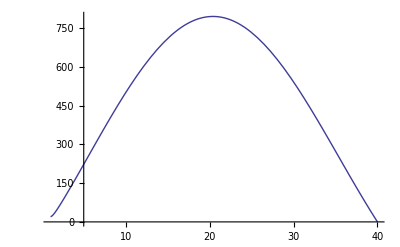

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.15+0.000001*I);
ie=0;While[ie<201,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5 +ie/200; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
qscals[ie]=qscal/mu;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[qscals[n],10],Re[witer[n]]},{n,0,200}];
t2r=Table[{N[qscals[n],10],Im[witer[n]]},{n,0,200}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

NDSolve::ndsz: At r == 1.04471, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {40} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At r == 1.04471, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {40} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At r == 1.04471, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {40} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.15+0.000001*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5 - ie/200; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
qscals[ie]=qscal/mu;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[qscals[n],10],Re[witer[n]]},{n,0,100}];
t2l=Table[{N[qscals[n],10],Im[witer[n]]},{n,0,100}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{5.,8.53157×10^-8},{4.95,8.15831×10^-8},{4.9,7.79709×10^-8},{4.85,7.44757×10^-8},{4.8,7.10955×10^-8},{4.75,6.78277×10^-8},{4.7,6.46697×10^-8},{4.65,6.16197×10^-8},{4.6,5.86739×10^-8},{4.55,5.58316×10^-8},{4.5,5.30894×10^-8},{4.45,5.04435×10^-8},{4.4,4.78947×10^-8},{4.35,4.54395×10^-8},{4.3,4.30749×10^-8},{4.25,4.07993×10^-8},{4.2,3.86101×10^-8},{4.15,3.65064×10^-8},{4.1,3.44848×10^-8},{4.05,3.25439×10^-8},{4.,3.06817×10^-8},{3.95,2.88954×10^-8},{3.9,2.71842×10^-8},{3.85,2.55458×10^-8},{3.8,2.39708×10^-8},{3.75,2.24788×10^-8},{3.7,2.10466×10^-8},{3.65,1.96802×10^-8},{3.6,1.83765×10^-8},{3.55,1.71341×10^-8},{3.5,1.59522×10^-8},{3.45,1.4828×10^-8},{3.4,1.37606×10^-8},{3.35,1.27475×10^-8},{3.3,1.17878×10^-8},{3.25,1.08794×10^-8},{3.2,1.00207×10^-8},{3.15,9.21865×10^-9},{3.1,8.44684×10^-9},{3.05,7.72832×10^-9},{3.,7.05338×10^-9},{2.95,6.42044×10^-9},{2.9,5.82785×10^-9},{2.85,5.27506×10^-9},{2.8,4.70586×10^-9},{2.75,4.27998×10^-9},{2.7,3.83544×10^-9},{2.65,3.42313×10^-9},{2.6,3.04433×10^-9},{2.55,2.6954×10^-9},{2.5,2.3755×10^-9},{2.45,2.08188×10^-9},{2.4,1.8177×10^-9},{2.35,1.57692×10^-9},{2.3,1.35989×10^-9},{2.25,1.1638×10^-9},{2.2,9.91363×10^-10},{2.15,8.45385×10^-10},{2.1,7.01192×10^-10},{2.05,5.82171×10^-10},{2.,4.78709×10^-10},{1.95,3.8862×10^-10},{1.9,3.12737×10^-10},{1.85,2.47309×10^-10},{1.8,1.9165×10^-10},{1.75,1.44113×10^-10},{1.7,9.14228×10^-11},{1.65,4.71295×10^-11},{1.6,-3.11574×10^-11},{1.55,-5.60061×10^-12},{1.5,-4.46767×10^-11},{1.45,-9.05072×10^-11},{1.4,-9.76961×10^-11},{1.35,-2.18449×10^-10},{1.3,-3.09356×10^-10},{1.25,-3.82853×10^-10},{1.2,-5.78548×10^-10},{1.15,-7.6339×10^-10},{1.1,-1.00926×10^-9},{1.05,-1.30732×10^-9},{1.,-1.66875×10^-9},{0.95,-2.10989×10^-9},{0.9,-2.663×10^-9},{0.85,-3.31139×10^-9},{0.8,-4.08376×10^-9},{0.75,-4.9958×10^-9},{0.7,-6.06721×10^-9},{0.65,-7.31775×10^-9},{0.6,-8.7693×10^-9},{0.55,-1.04464×10^-8},{0.5,-1.23709×10^-8},{0.45,-1.46302×10^-8},{0.4,-1.71013×10^-8},{0.35,-1.99658×10^-8},{0.3,-2.32078×10^-8},{0.25,-2.68666×10^-8},{0.2,-3.09907×10^-8},{0.15,-3.56351×10^-8},{0.1,-4.07931×10^-8},{0.05,-4.6586×10^-8},{0.,-5.28605×10^-8}}

```mathematica
(*The imaginary part vs the radius*)
```

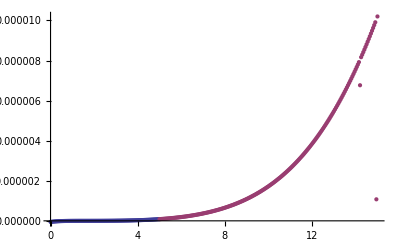

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

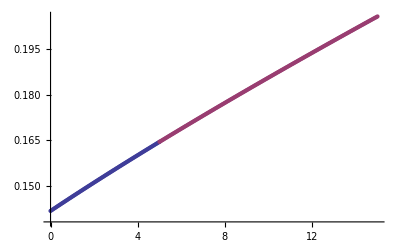

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/q/mu0.1/r=40/Q=0.999/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/q/mu0.1/r=40/Q=0.999/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/q/mu0.1/r=40/Q=0.999/R.dat

/home/h/skoli/pt/rnef/mathematica/q/mu0.1/r=40/Q=0.999/I.dat